```mathematica
CountCarriesPerDigit[list_,p_,q_] := Module[
{result,  i,carry=0,val},
result=Table[0,{i, 0,q-1}];
For [i=Length[list],i>0,i--,
val=list[[i]]*p + carry;
carry=Mod[val,q];
result[[carry+1]]=result[[carry+1]] +1;
];
result
]
```

```mathematica
CountCarriesPerDigit[IntegerDigits[2^100,3],2,3]
```

{26,16,23}

{{0,0,0,0,1/4,1/2},{0,1/2,1/2,1/3,0,1/4},{1,0,1/2,1/3,1/2,1/4}}

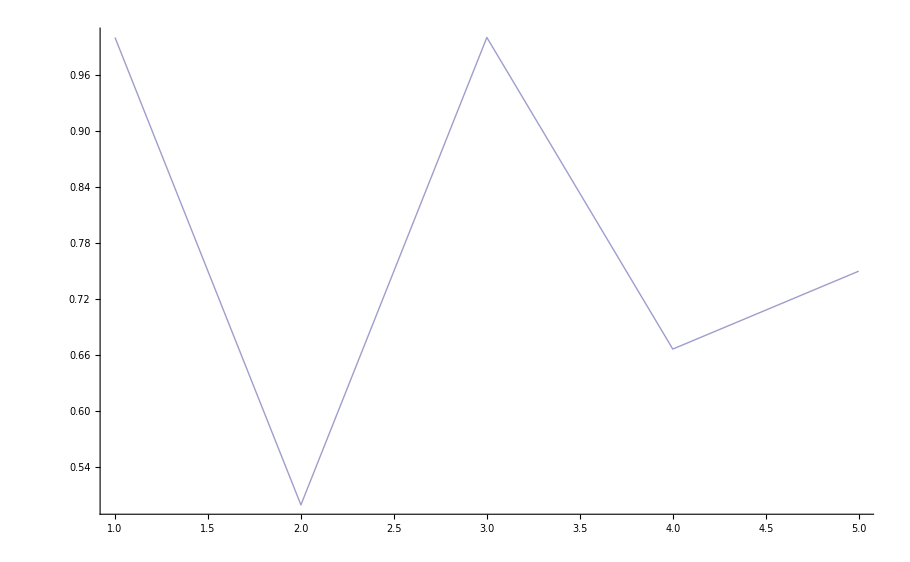

```mathematica
With [
{p=2,q=3,MAX=5},
Module[
{PerDigit=Table[{},{i,0,q-1}]},
Monitor[
Table[
With[{ All = CountCarriesPerDigit[IntegerDigits[p^i,q],p,q], next=IntegerLength[p^(i+1),q]},
Table[AppendTo[PerDigit[[j]], All[[j]]/next],{j,1,q}]
],
{i,0,MAX}
],
i];
Print[PerDigit];
ListPlot[Table[Sum[PerDigit[[i]][[j]],{i,1,q}],{j,1,MAX}],
GridLines->{Automatic,{{1/q,{Thick,Red}}}},
PlotStyle->Opacity[0.5],
Joined->True
]
]
]
```

```mathematica
CarriesVector[current_,p_,q_] := Module[
{result,  i,carry=0,val,list},
list=Reverse[IntegerDigits[current,q]];
result={};
For [i=1,i<=Length[list],i++,
val=list[[i]]*p + carry;
carry=Quotient[val,q];
AppendTo[result,carry];
];
If[carry > 0,
AppendTo[result, carry] 
];
Reverse[result]
]
```

```mathematica
CarriesVector2[current_,p_,q_] := Module[
{result,  i,carry=0,val,list},
list=IntegerDigits[current,q];
result={};
For [i=1,i<=Length[list],i++,
val=list[[i]]*p + carry;
carry=Mod[val,q];
PrependTo[result,carry];
];
(*If[carry > 0,
PrependTo[result, carry] 
];*)
result
]
```

```mathematica
CarriesVector[2^7,2,3]
```

{4,1}

{1,0}

{4,1}

{3,1}

{3,1}

{1,1,1,1,0,1}

```mathematica
IntegerDigits[2^7,3]
```

{1,1,2,0,2}

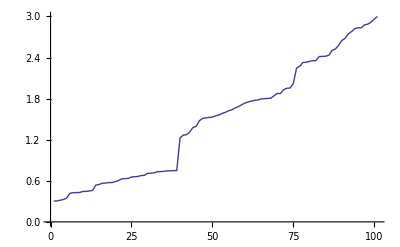

```mathematica
ListLinePlot[
Sort[Table[FromDigits[CarriesVector[2^i,2,3],3]/2^(i+1),{i,0,100}]]
]
```

```mathematica
IntegerD2^10
```

1024

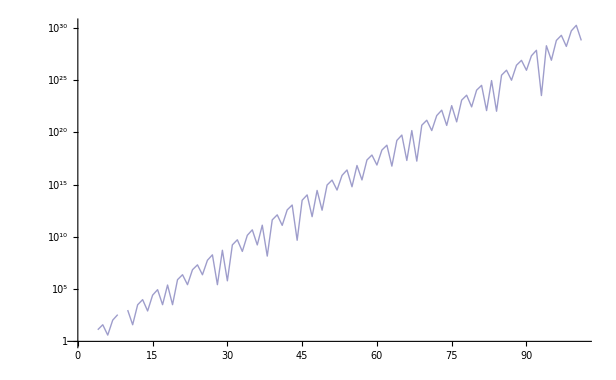

```mathematica
With [
{p=2,q=3,MAX=100},
Module[
{perDigit},
perDigit=Monitor[
Table[
FromDigits[CarriesVector[p^i,p,q],q],
{i,0,MAX}
],
i];
ListLogPlot[perDigit,
PlotStyle->Opacity[0.5],
Joined->True
]
]
]
```

```mathematica
RepeatDigitsCarry[n_,p_,q_]:=Module[{startPattern,  start = 0, current, digits, bad, tail},
digits = CarriesVector2[p^0,p,q];
startPattern = Take[PadLeft[digits,n],-n];
Print["Start pattern " <> ToString[startPattern]];
current = start +1;
digits = CarriesVector2[p^current,p,q];
tail = Take[PadLeft[digits,n],-n];
bad=0;
Print["digit - " <> ToString[current]<> " --> " <> ToString[tail]];
While[tail ≠ startPattern,
current +=1;
digits = CarriesVector2[p^current,p,q];
tail = Take[PadLeft[digits,n],-n];
Print["digit - " <> ToString[current]<> " --> " <> ToString[tail]];
];
Print["Found repeating pattern after " <> ToString[current- start+1]];
Return[current-start]
]
```

```mathematica
Clear[RepeatDigitsCarry]
```

```mathematica
RepeatDigitsCarry[6,2,3]
```

416

```mathematica
CarriesVector[1,2,3]
```

{2,0}

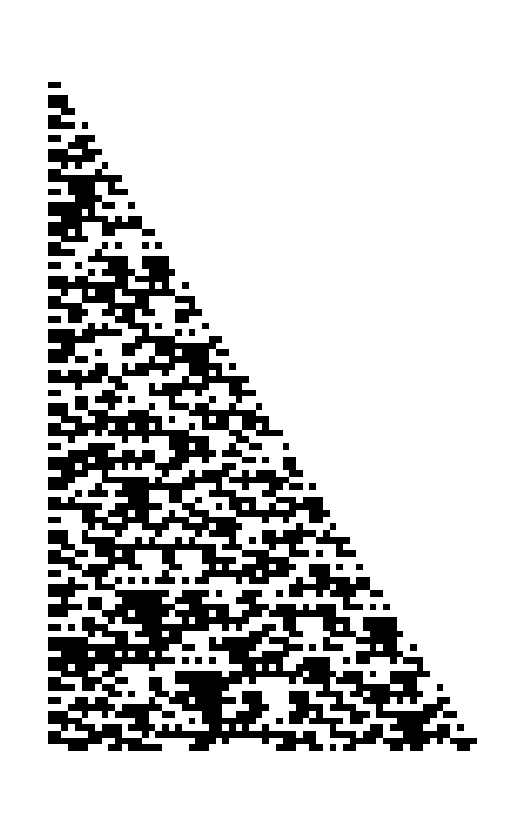

```mathematica
ArrayPlot[
Table[CarriesVector[2^i,2,3],{i,0,100}],
ColorRules->{0->White,1->Black,2->Darker[Green]}
]
```

```mathematica
CarriesVector[IntegerDigits[2^6,3],2,3]
```

{0,{1},{0},{0}}

```mathematica
Table[Reverse[IntegerDigits[2^i+FromDigits[CarriesVector[IntegerDigits[2^i,3],2,3],3],3]],{i,0,200}]
```

```mathematica
ArrayPlot[
Table[Take[
CarriesVector[2^i,2,3]
,2],{i,0,200}],
ColorRules->{0->White,1->Black,2->Darker[Green]}
]
```

```mathematica
Table[CarriesVector[IntegerDigits[2^i,3],2,3],{i,0,200}]
```

{{0},{0},«198»,{{2},{2},{1},{1},{1},{2},{2},{2},{1},{1},{1},{2},{0},{1},{0},{2},{1},{0},{2},{2},{0},{0},{0},{1},{0},{0},{0},{2},{1},{2},{0},{0},{2},{1},{1},{1},{0},{2},{1},{1},{2},{2},{2},{2},{0},{2},{1},{1},{2},{0},{0},{2},{0},{2},{0},{0},{0},{1},{2},{2},{1},{1},{0},{1},{1},{2},{0},{0},{2},{2},{2},{0},{0},{0},{0},{1},{2},{0},{0},{0},{1},{1},{2},{0},{1},{0},{0},{2},{0},{0},{1},{1},{0},{2},{0},{1},{1},{2},{0},{2},{2},{2},{2},{2},{2},{0},{1},{0},{1},{2},{2},{0},{0},{2},{2},{2},{1},{0},{2},{1},{2},{2},{2},{1},{1},{2},0}}

```mathematica
DGraph4[list_,d_] := Module[
{result={}, i, doubled={},carry=0,val},
For [i=1,i<=Length[list],i++,
AppendTo[doubled,list[[i]]*2];
AppendTo[result,{{"N" <> ToString[d],i}->{"N" <> ToString[d+1],i},Blue}]
];
For [i=Length[doubled],i>0,i--,
val=doubled[[i]] + carry;
If[val≥3,AppendTo[result,{{"N" <> ToString[d+1],i}->{"N" <> ToString[d+1],i+1},Directive[Red, Thick]}]];
carry=Mod[val,3];
];
result
]
```